```mathematica
gs=GeometricScene[{"A","B","C","O"},{Triangle[{"A","B","C"}],CircleThrough[{"A","B","C"},"O"],"O"==Midpoint[{"A","C"}],Style[Line[{"A","B"}],Orange],Style[Line[{"B","C"}],Orange]}];
```

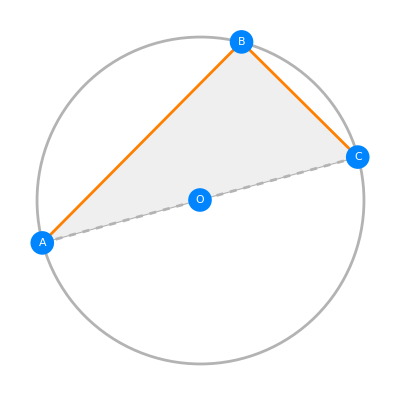

```mathematica
RandomInstance[gs]
```

```mathematica
c=FindGeometricConjectures[gs]
```

```mathematica
c["Conclusions"]
```

{GeometricAssertion[{Line[{B,A}],Line[{C,B}]},Perpendicular],PlanarAngle[{A,B,C}]==90 °}